```mathematica
FullSimplify[Binomial[n,m]==Binomial[n-1,m]+Binomial[n-1,m-1],n≠0&&m≠0]
```

True

```mathematica
FullSimplify[Binomial[n,m]==Binomial[n-1,m]+Binomial[n-1,m-1],n==0&&m==0]
```

False

```mathematica
FullSimplify[PascalBinomial[n,m]==PascalBinomial[n-1,m]+PascalBinomial[n-1,m-1],n==0&&m==0]
```

True

```mathematica
FullSimplify[Binomial[n,m]==Binomial[n,n-m]]
```

True

```mathematica
Binomial[n+ 90,n]
```

Binomial[90+n,n]

```mathematica
Binomial[n+ 1680,n]
```

Binomial[1680+n,n]

```mathematica
FunctionExpand[Binomial[n+6,n],n∈Integers]
```

1/720 (1+n) (2+n) (3+n) (4+n) (5+n) (6+n)

```mathematica
FullSimplify[Binomial[n+1,k+1]/Binomial[n,k]]
```

(1+n)/(1+k)

```mathematica
FunctionExpand[Binomial[n,k]]
```

Gamma[1+n]/(Gamma[1+k] Gamma[1-k+n])

```mathematica
∑_(k=0)^n (-1)^k Binomial[n,k]
```

n

```mathematica
∑_(j=k)^n Binomial[n,j] Binomial[j,k]
```

2^(-k+n) Binomial[n,k]

```mathematica
∑_(k=1)^∞ 1/Binomial[2 k,k]
```

1/27 (9+2 √3 π)

```mathematica
∑_(k=0)^∞ Binomial[n,k] x^k
```

(1+x)^n

```mathematica
DifferenceRootReduce[Binomial[k,z],k]
```

[k]

```mathematica
DifferenceRootReduce[Binomial[z,k],k]
```

[k]

```mathematica
GeneratingFunction[Binomial[k,n],n,x]
```

(1+x)^k

```mathematica
ExponentialGeneratingFunction[Binomial[k,n],n,x]
```

Hypergeometric1F1[-k,1,-x]

```mathematica
With[{n=8},
Graph[Flatten[Table[{b[i,j]<->b[i+1,j],b[i,j]<->b[i+1,j+1],b[i+1,j]<->b[i+1,j+1]},{i,0,n-1},{j,0,i}]],VertexCoordinates->{b[i_,j_]:>{(n+1)/2-i/2+j,-i}},VertexLabels->{b[i_,j_]:>Placed[Binomial[i,j],Center]},]]
```

-Graphics-

```mathematica
With[{n=6},Graph[Flatten[Table[{b[i,j]<->b[i+1,j],b[i,j]<->b[i+1,j+1],b[i+1,j]<->b[i+1,j+1]},{i,n-1,-n-1,-1},{j,-n+i UnitStep[i]-UnitStep[-1-i],n+i UnitStep[-i]+UnitStep[-1-i]}]],VertexCoordinates->{b[i_,j_]:>{(n+1)/2-i/2+j,-i}},]]
```

-Graphics-

```mathematica
With[{n=6},Graph[Flatten[Table[{b[i,j]<->b[i+1,j],b[i,j]<->b[i+1,j+1],b[i+1,j]<->b[i+1,j+1]},{i,n-1,-n-1,-1},{j,-n+i UnitStep[i]-UnitStep[-1-i],n+i UnitStep[-i]+UnitStep[-1-i]}]],VertexCoordinates->{b[i_,j_]:>{(n+1)/2-i/2+j,-i}},]]
```

-Graphics-

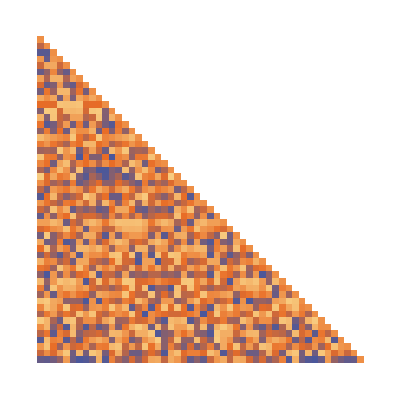

```mathematica
ArrayPlot[Table[Mod[Binomial[i,j],Pi],{i,50},{j,i}],PlotTheme->"Scientific"]
```

```mathematica
Block[{n=4},Table[(-1)^(i+j)(i+j-1)Binomial[n+i-1,n-j]Binomial[n+j-1,n-i]Binomial[i+j-2,i-1]^2,{i,n},{j,n}]]//MatrixForm
```

(16 | -120 | 240 | -140
-120 | 1200 | -2700 | 1680
240 | -2700 | 6480 | -4200
-140 | 1680 | -4200 | 2800)

```mathematica
Inverse[]
```

-Graphics-

```mathematica
DensityPlot[Arg[Nest[Binomial[#,#/2]&,x+I y,3]],{x,-1,-0.9},{y,-0.06,0.06},Exclusions->{},MaxRecursion->4]//Quiet
```

-Graphics-

```mathematica
DensityPlot[Arg[Binomial[(x+I y),1/(x+I y)]],{x,-1/2,1/2},{y,-1/2,1/2},Exclusions->{},MaxRecursion->4]//Quiet
```

-Graphics-

```mathematica
DensityPlot[Arg[Binomial[4.1 Exp[I ϕ1],2.2 Exp[I ϕ2]]],{ϕ1,-Pi,Pi},{ϕ2,-Pi,Pi},Exclusions->{},MaxRecursion->4]
```

-Graphics-

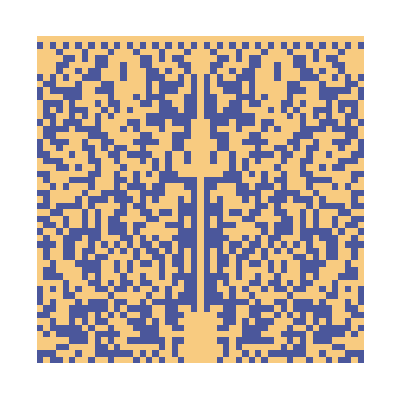

```mathematica
Block[{$MaxExtraPrecision=1000},ArrayPlot[Table[Mod[Im@Round[Binomial[x +I y,x ]],2],{x,0,50},{y,-25,25}],PlotTheme->"Scientific"]]
```